### Mathematica as a standalone application

The Import/Export of data can be solved in different ways using different technology.

Direct import of data from file using standard formats

Database connection

Internal computable data sources

WolframAlpha link

#### Example 1

Using Import/Export is most common way users exchange data from external sources and Mathematica (and viceversa)

```mathematica
$ImportFormats
```

```mathematica
$ExportFormats
```

Basic syntax of Import

Import["file", format]: Import data from a file according to a specific format

Import["file", {format, elements}]: import only specified elements

Import["http://url",…]: import from any URL using HTTP, HTTPS or FTP protocol

Many times you can also avoid to specify the file’s format, Import does recognize it automatically

```mathematica
Import["ExampleData/mri.pxr"]
```

```mathematica
Import["ExampleData/cities.xlsx"]
```

```mathematica
Import["http://earthobservatory.nasa.gov/images/imagerecords/2000/2903/Sicily_AMO_2002301_lrg.jpg",ImageSize->{600,Automatic}]
```

```mathematica
Import["http://photojournal.jpl.nasa.gov/jpeg/PIA12708.jpg"]
```

#### Example 2

Connection with database in another important way to work with data. 
The package DatabaseLink provides some macro useful to make any kind of queries to a database. See main commands here

#### Example 3

Mathematica has another unique feature: it provides internal computable data sources in many key fields.

#### ChemicalData

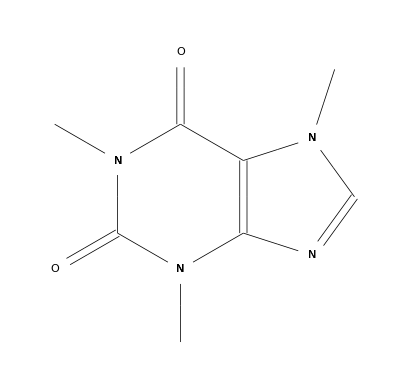

```mathematica
ChemicalData["Caffeine"]
```

To know whichproperties can be required for a particular element, use the second argument “Properties”

```mathematica
ChemicalData["Caffeine", "Properties"]
```

{AcidityConstant,AcidityConstants,AdjacencyMatrix,AlternateNames,AtomPositions,AutoignitionPoint,BeilsteinNumber,BoilingPoint,BondTally,CASNumber,CHColorStructureDiagram,CHStructureDiagram,CIDNumber,Codons,ColorStructureDiagram,CombustionHeat,CompoundFormulaDisplay,CompoundFormulaString,CriticalPressure,CriticalTemperature,Density,DensityGramsPerCC,DielectricConstant,DOTHazardClass,DOTNumbers,EdgeRules,EdgeTypes,EGECNumber,ElementMassFraction,ElementTally,ElementTypes,EUNumber,FlashPoint,FlashPointFahrenheit,FormalCharges,FormattedName,GmelinNumber,HBondAcceptorCount,HBondDonorCount,HenryLawConstant,HildebrandSolubility,HildebrandSolubilitySI,InChI,IonEquivalents,Ions,IonTally,IsoelectricPoint,IsomericSMILES,IUPACName,LogAcidityConstant,LowerExplosiveLimit,MDLNumber,MeltingBehavior,MeltingPoint,Memberships,MolarVolume,MolecularFormulaDisplay,MolecularFormulaString,MolecularWeight,MoleculePlot,Name,NFPAFireRating,NFPAHazards,NFPAHealthRating,NFPALabel,NFPAReactivityRating,NonHydrogenCount,NonStandardIsotopeCount,NonStandardIsotopeNumbers,NonStandardIsotopeTally,NSCNumber,OdorThreshold,OdorType,PartitionCoefficient,pH,Phase,RefractiveIndex,Resistivity,RotatableBondCount,RTECSClasses,RTECSNumber,SideChainAcidityConstant,SMILES,Solubility,SolubilityType,SpaceFillingMoleculePlot,StandardName,StructureDiagram,SurfaceTension,TautomerCount,ThermalConductivity,TopologicalPolarSurfaceArea,UpperExplosiveLimit,VanDerWaalsConstants,VaporDensity,VaporizationHeat,VaporPressure,VaporPressureTorr,VertexCoordinates,VertexTypes,Viscosity}

```mathematica
ChemicalData["Caffeine", "MoleculePlot"]
```

-Graphics3D-

One of the most interesting aspect of computable data sources, as the name itself says, is that such data are ready to be used in any kind of Mathematica computation, report, graphics, dynamic interface, etc.

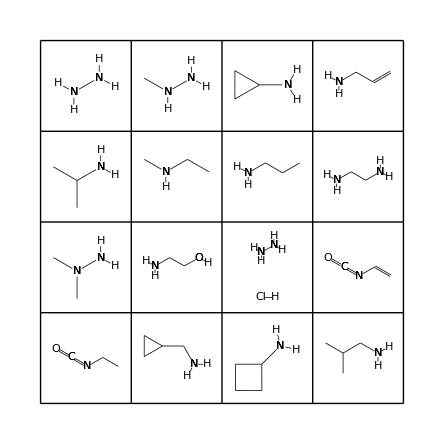

```mathematica
GraphicsGrid[Partition[Show[ChemicalData[#],ImageSize->Tiny]&/@Take[ChemicalData["Amines"],16],4],Frame->All]
```

```mathematica
Manipulate[ListPlot[Table[{ChemicalData[chem,"Density"],ChemicalData[chem,"BoilingPoint"]},{chem,ChemicalData[grp]}],AxesLabel->{"density","boiling point"}],{{grp,"Alkanes","chemical class"},ChemicalData["Classes"]}]
```

#### WeatherData

```mathematica
WeatherData["Trieste"]
```

LIVT

```mathematica
WeatherData["LIVT", "Properties"]
```

{AlternateStandardNames,CloudCoverFraction,CloudHeight,CloudTypes,Conditions,Coordinates,DewPoint,Elevation,Humidity,Latitude,Longitude,MaxTemperature,MaxWindSpeed,MeanDewPoint,MeanHumidity,MeanPressure,MeanStationPressure,MeanTemperature,MeanVisibility,MeanWindChill,MeanWindSpeed,Memberships,MinTemperature,NCDCID,PrecipitationAmount,PrecipitationRate,PrecipitationTypes,Pressure,PressureTendency,SnowAccumulation,SnowAccumulationRate,SnowDepth,StationName,StationPressure,Temperature,TotalPrecipitation,Visibility,WBANID,WindChill,WindDirection,WindGusts,WindSpeed,WMOID}

```mathematica
WeatherData["LIVT", "Temperature", "DateValue"]
```

{{2013,3,11,8,0,0},10.2}

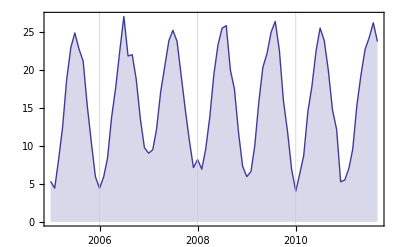

```mathematica
DateListPlot[WeatherData["LIVT", "MeanTemperature", {{2005,1,1},{2011,9,30}, "Month"}], Joined->True,Filling->Bottom]
```

#### Example 4

WolframAlpha is directly available from inside Mathematica.

do an ideal gas law computation

ideal gas law 2.2mol, 2.0atm, 500K

compute photon energy given wavelength

photon energy 435nm

WolframAlpha has trillions of information stored, from hundreds of databases covering many different subjects

how far is Trieste from London